```mathematica
ListPlot3D[data[[All,{1,2,3}]],PlotRange->All,ImageSize->800]
```

-Graphics3D-

### One data

```mathematica
datai=Table[Sort[Import["/Users/wanglong/Dropbox/Datas/NBPrf/hydra/time."~~ToString[i]~~".dat","table"]],{i,{0,0.05,0.1,0.2}}];
label=Import["/Users/wanglong/Dropbox/Datas/NBPrf/hydra/label","Table"][[1]];
```

```mathematica
nsl={1,2,4,8,16};
nbin={0,0.05,0.1,0.2};
tscale=2;
k=2;
data=Table[Table[datai[[j,i,1;;2]]~Join~(datai[[j,i,3;;]]/tscale),{i,Length@datai[[j]]}],{j,Length@datai}];
ns2=(nbin[[k]]+1)*{16000,32000,64000,128000,256000,512000,1024000};
eplinear[d_,j_]:=Table[Select[d,#[[2]]==i&][[1,j]]/x,{i,ns2}]
ttpp[d_,j_]:=Table[Select[d,#[[1]]==i&][[All,{2,j}]],{i,nsl}]
plist2[d_,j_]:=Table[Select[d,#[[2]]==i&][[All,{1,j}]],{i,ns2}]
s1style={Black,Purple,Blue,Green,Orange,Red};
s2style={Black,Purple,Blue,Green,Orange,Yellow,Red};
lplot=Table[label[[j]]->Row@{ListLogLogPlot[ttpp[data[[k]],j],PlotLegends->LineLegend[s1style,ToString/@nsl],PlotStyle->s1style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,AxesLabel->label[[{2,j}]]],ListLogLogPlot[plist2[data[[k]],j],PlotLegends->LineLegend[s2style,ToString/@ns2],PlotStyle->s2style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,Epilog->First@LogLogPlot[eplinear[data[[k]],j],{x,1,16},PlotStyle->Dotted],AxesLabel->label[[{1,j}]]]},{j,3,Length@label,1}];
```

```mathematica
TabView[lplot]
```

1234567891011121314151617181920212223242526272829303132333435363738

```mathematica
Export["/Users/wanglong/data/NBPrf/time_b10.eps",label[[3]]/.lplot]
```

/Users/wanglong/data/NBPrf/time_b10.eps

```mathematica
out=MapThread[Prepend,{Prepend[ttpp[data[[k]],3][[All,All,2]],ttpp[data[[k]],3][[1,All,1]]],{"N"}~Join~nsl}];
```

```mathematica
Export["/Users/wanglong/data/NBPrf/time.txt",out]
```

/Users/wanglong/data/NBPrf/time.txt

#### Old

```mathematica
ddd=Cases[data,{p_,n_,tt_,tinit_,tint_,treg_,tirr_,tintb_,tnewt_,tcopyx_,tmov_,tsub1_,tsub2_,tks_,tadj_,tsube_,tgpucomm_,tgrcalc_,tgrcalc2_,tgpu_,tprb_,tnbi_,tbar_,tbarnb_,tbarreg_,x___}->{p,n,tt-tinit,treg,tnbi,tprb,tintb,tnewt,tcopyx,tmov,tsub1,tsub2,tks,tadj,tbar}];
ddlabel=label[[{1,2,3,6,22,21,8,9,10,11,12,13,14,15,23}]];
timestep=2;
dtot=Cases[ddd,{p_,n_,tt_,t___}->{p,n,tt/timestep}];
dreg=Cases[ddd,{p_,n_,tt_,treg_,t___}->{p,n,treg/timestep}];
dnbi=Cases[ddd,{p_,n_,tt_,treg_,tnbi_,t___}->{p,n,tnbi/timestep}];
dprd=Cases[ddd,{p_,n_,tt_,treg_,tnbi_,tprb_,t___}->{p,n,tprb/timestep}];
dadj=Cases[ddd,{p_,n_,tt_,treg_,tnbi_,tprb_,t___,tadj_,tbar_}->{p,n,tadj/timestep}];
dcomm=Cases[ddd,{p_,n_,tt_,treg_,tnbi_,tprd_,tintb_,tnewt_,tcopyx_,tmov_,tsub1_,tsub2_,t___}->{p,n,(tmov+tsub1+tsub2)/timestep}];
dbar=Cases[ddd,{p_,n_,tt_,treg_,tnbi_,tprb_,t___,tbar_}->{p,n,tbar/timestep}];
dd={dtot,dreg,dnbi,dprd,dadj,dcomm,dbar};
dlabel={"T_tot","T_reg","T_nbi","T_pred","T_adj","T_com","T_bar"};
plist1[d_]:=Table[Select[d,#[[1]]==i&][[All,2;;3]],{i,nsl}];
plist2[d_]:=Table[Select[d,#[[2]]==i&][[All,{1,3}]],{i,ns2}]
eplinear[d_]:=Table[#1*#2&@@Select[d,#[[2]]==i&][[1,{1,3}]]/x,{i,ns2}];
```

```mathematica
d321m=Select[ddd,#[[1;;2]]=={32,1024000}&][[1]];
fraction=Grid[Table[{ddlabel[[i]],d321m[[i]]/d321m[[3]]},{i,3,Length@d321m}],Frame->All]
```

ttot | 1.
treg | 0.118859
ttnbi | 0.150745
tprednb | 0.0970879
ttintb | 0.0574555
ttnewt | 0.0669374
ttcopyx | 0.0266764
tmov | 0.0618206
tsub | 0.0937897
tsub2 | 0.0356688
tks | 0.00066699
tadj | 0.0111981
ttbar | 0.284872

```mathematica
Plus@@Table[d321m[[i]]/d321m[[3]],{i,4,Length@d321m}]
```

1.00578

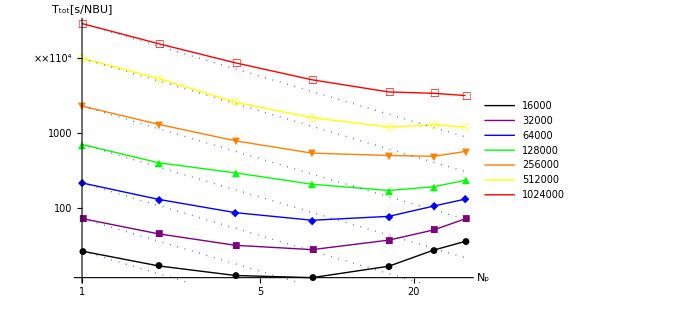
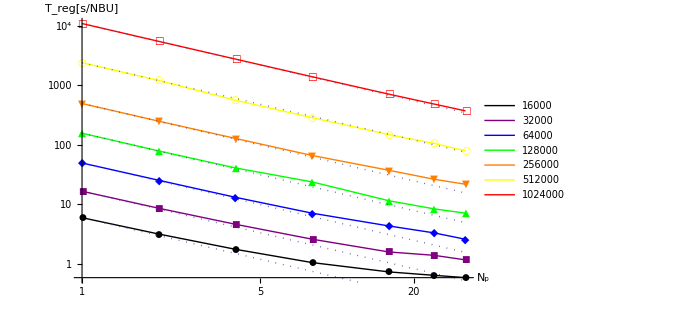
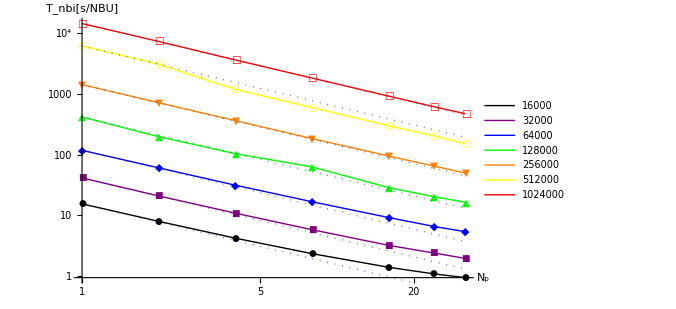
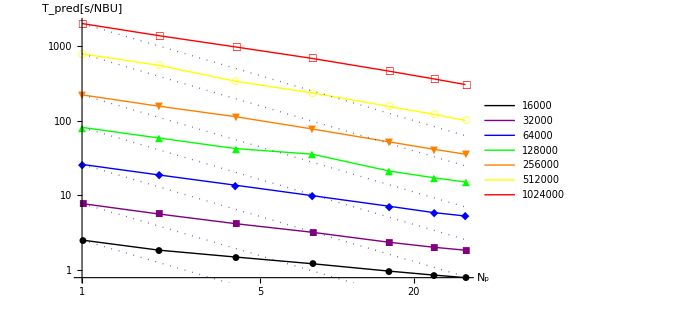
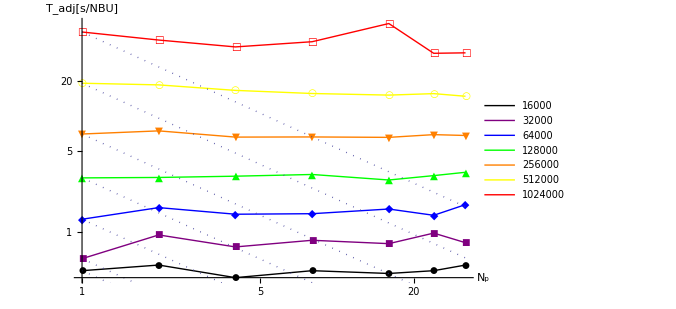
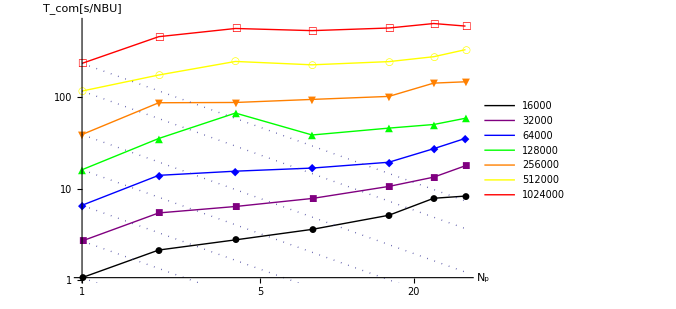
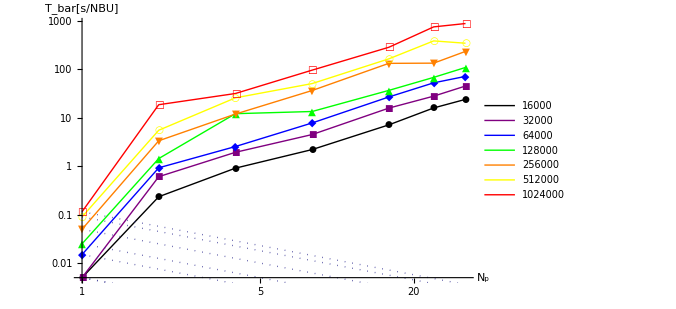

```mathematica
exp1=Table[ListLogLogPlot[plist1[dd[[j]]],PlotLegends->LineLegend[s1style,#&@(ToString/@nsl)],PlotStyle->s1style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,AxesLabel->{"N",dlabel[[j]]~~"[s/NBU]"}],{j,7}];
exp2=Table[ListLogLogPlot[plist2[dd[[j]]],PlotLegends->LineLegend[s2style,#&@(ToString/@ns2)],PlotMarkers->Automatic,PlotStyle->s2style,PlotRange->All,Epilog->First@LogLogPlot[eplinear[dd[[j]]],{x,1,32},PlotStyle->Dotted],ImageSize->500,Joined->True,AxesLabel->{"N_p",dlabel[[j]]~~"[s/NBU]"}],{j,7}]
```

#### Pie Chart

```mathematica
k=2;
columnlist={1,2,6,7,8,9,11,12,13,14,15,17,18,28,29,30,31,32,33,34,35,36,37,38};
datp=data[[k,All,columnlist]];
nbin={0,0.05,0.1,0.2};
nsp=(nbin[[k]]+1)*{16000,32000,64000,128000,256000,512000,1024000};
labelp=label[[columnlist[[3;;]]]];
pcolor={Black,Red,Green,Yellow,White,Blue,Orange,Purple,Gray,Cyan,Magenta,Brown,Pink,LightRed,LightBlue,LightYellow,LightBrown,LightMagenta,LightGreen,LightOrange,LightPurple,LightCyan};
exp5=Column[{"From inside to outside: N_proc = 1, 2, 4, 8",Grid[Partition[
Table[Column[{"N="~~ToString[i/1000]~~"K",
PieChart[Select[datp,#[[2]]==i&][[All,3;;]],ChartStyle->pcolor,ImageSize->300]},Center],{i,nsp[[;;-2]]}],3]],Column[{"N="~~ToString[nsp[[-1]]/1000]~~"K",
PieChart[Select[datp,#[[2]]==nsp[[-1]]&][[All,3;;]],ChartLegends->labelp,ChartStyle->pcolor,ImageSize->300]},Center]},Center]
```

From inside to outside: N_proc = 1, 2, 4, 8
N=16.8K
-Graphics- | N=33.6K
-Graphics- | N=67.2K
-Graphics-
N=134.4K
-Graphics- | N=268.8K
-Graphics- | N=537.6K
-Graphics-
N=1075.2K
-Graphics-

```mathematica
Export["/Users/wanglong/data/NBPrf/piechart_b10.eps",exp5]
```

/Users/wanglong/data/NBPrf/piechart_b10.eps

#### Old

```mathematica
columnlist={6,22,21,8,9,10,11,12,13,14,15,23};
exp3=Column[{"From inside to outside: N = 16k, 32k, 64k, 128k, 256k, 512k, 1M",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[data,#[[1]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,nsl}]},Center]
exp4=Column[{"From inside to outside: N_proc = 1, 2, 4, 8, 16, 24, 32",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[data,#[[2]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,ns2}]},Center]
```

From inside to outside: N = 16k, 32k, 64k, 128k, 256k, 512k, 1M
{N_proc=1
-Graphics-,N_proc=2
-Graphics-,N_proc=4
-Graphics-,N_proc=8
-Graphics-,N_proc=16
-Graphics-,N_proc=24
-Graphics-,N_proc=32
-Graphics-}

From inside to outside: N_proc = 1, 2, 4, 8, 16, 24, 32
{N_proc=16000
-Graphics-,N_proc=32000
-Graphics-,N_proc=64000
-Graphics-,N_proc=128000
-Graphics-,N_proc=256000
-Graphics-,N_proc=512000
-Graphics-,N_proc=1024000
-Graphics-}

### GPU

```mathematica
gpudata=Table[Import["/Users/wanglong/Dropbox/Datas/NBPrf/hydra/reg."~~ToString@i~~".dat","Table"][[All,{2,4,10,12,14,16,18,20,22,24}]],{i,{0,0.05,0.1,0.2}}];
gpulabel={"N","N_proc","N_send","N_grav","<N_i>","T_send[sec.]","T_grav[sec.]","T_nb[sec.]","T_out[sec.]","Perf.[Gflops]"};
```

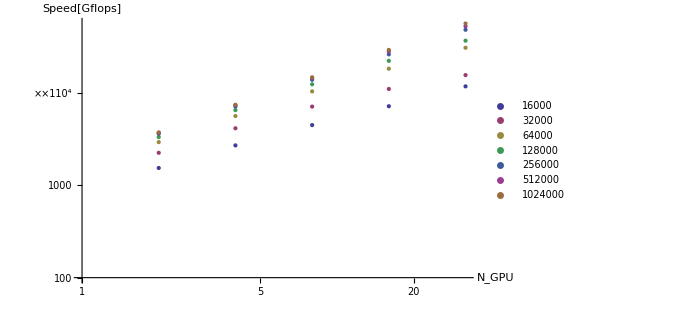

```mathematica
k=1;
nsl={1,2,4,8,16};
nbin={0,0.05,0.1,0.2};
ns2=(nbin[[k]]+1)*{16000,32000,64000,128000,256000,512000,1024000};
plotdat=Table[{i,Table[{j*2,Plus@@(Select[Select[gpudata[[k]],#[[1]]==i&][[All,{2,10}]],#[[1]]==j&][[All,2]])},{j,nsl}]},{i,ns2}];
ListLogLogPlot[plotdat[[All,2]],PlotLegends->plotdat[[All,1]],ImageSize->500,AxesLabel->{"N_GPU","Speed[Gflops]"},AxesOrigin->{0,100}]
```

```mathematica
exportdata=Prepend[MapThread[Prepend,{Table[plotdat[[All,2,i,2]],{i,Length@plotdat[[1,2]]}],2*nsl}],Prepend[plotdat[[All,1]],"N_{GPU}"]];
```

```mathematica
Export["/Users/wanglong/data/NBPrf/reg.reduce.txt",exportdata]
```

/Users/wanglong/data/NBPrf/reg.reduce.txt

### Two data

```mathematica
data=Sort[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/mpigpu/time.1","Table"]];
datac=Sort[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/mpi/time.1","Table"]];
label=Import["/Users/wanglong/Dropbox/Datas/Nb6Test/label","Table"][[1]];
```

```mathematica
nsl={1,2,4,8,16,24};
ns2={16000,32000,64000,128000,256000};
eplinear[d_,j_]:=Table[Select[d,#[[2]]==i&][[1,j]]/x,{i,{16000,32000,64000,128000,256000}}]
ttpp[d_,j_]:=Table[Select[d,#[[1]]==i&][[All,{2,j}]],{i,nsl}];
plist2[d_,j_]:=Table[Select[d,#[[2]]==i&][[All,{1,j}]],{i,ns2}]
p1style=Flatten[Transpose@Table[{i,{i,Dashed}},{i,{Black,Purple,Blue,Green,Yellow,Orange,Red}}],1];
p2style=Flatten[Transpose@Table[{i,{i,Dashed}},{i,{Black,Blue,Green,Yellow,Red}}],1];
TabView[Table[label[[j]]->Row@{ListLogLogPlot[ttpp[data,j]~Join~ttpp[datac,j],PlotLegends->LineLegend[p1style,Flatten[{#"GPU",#}&@(ToString/@nsl)]],PlotStyle->p1style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,AxesLabel->label[[{2,j}]]],ListLogLogPlot[plist2[data,j]~Join~plist2[datac,j],PlotLegends->LineLegend[p2style,Flatten[{#"GPU",#}&@(ToString/@ns2)]],PlotStyle->p2style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,Epilog->First@LogLogPlot[eplinear[data,j]~Join~eplinear[datac,j],{x,1,32},PlotStyle->Dotted],AxesLabel->label[[{2,j}]]]},{j,3,16,1}]]
```

1234567891011121314

```mathematica
ddd=Cases[data,{p_,n_,tt_,treg_,tirr_,tpt_,tint_,tinit_,tks_,tcom_,tadj_,tmov_,tprb_,tsub1_,tsub2_,x___}->{p,n,tt-tinit,treg,tirr,tsub1,tsub2}];
dddc=Cases[datac,{p_,n_,tt_,treg_,tirr_,tpt_,tint_,tinit_,tks_,tcom_,tadj_,tmov_,tprb_,tsub1_,tsub2_,x___}->{p,n,tt-tinit,treg,tirr,tsub1,tsub2}];
timestep=1;
```

```mathematica
dtot=Cases[ddd,{p_,n_,tt_,t___}->{p,n,tt/timestep}];
dreg=Cases[ddd,{p_,n_,tt_,treg_,t___}->{p,n,treg/timestep}];
dirr=Cases[ddd,{p_,n_,tt_,treg_,tirr_,t___}->{p,n,tirr/timestep}];
dmov=Cases[ddd,{p_,n_,tt_,treg_,tirr_,tsub1_,tsub2_}->{p,n,(tsub1+tsub2)/timestep}];
dtotc=Cases[dddc,{p_,n_,tt_,t___}->{p,n,tt/timestep}];
dregc=Cases[dddc,{p_,n_,tt_,treg_,t___}->{p,n,treg/timestep}];
dirrc=Cases[dddc,{p_,n_,tt_,treg_,tirr_,t___}->{p,n,tirr/timestep}];
dmovc=Cases[dddc,{p_,n_,tt_,treg_,tirr_,tsub1_,tsub2_}->{p,n,(tsub1+tsub2)/timestep}];
dd={dtot,dreg,dirr,dmov};
ddc={dtotc,dregc,dirrc,dmovc};
dlabel={"Ttot","Treg","Tirr","Tsub"};
```

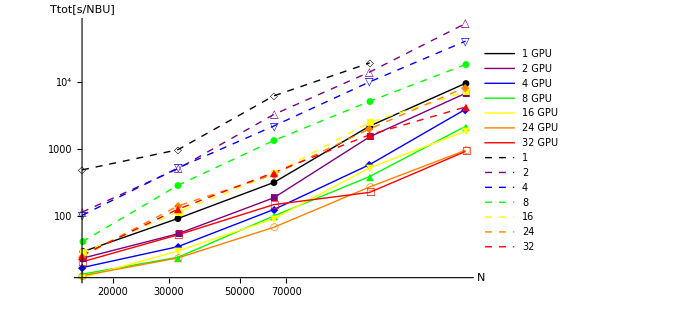
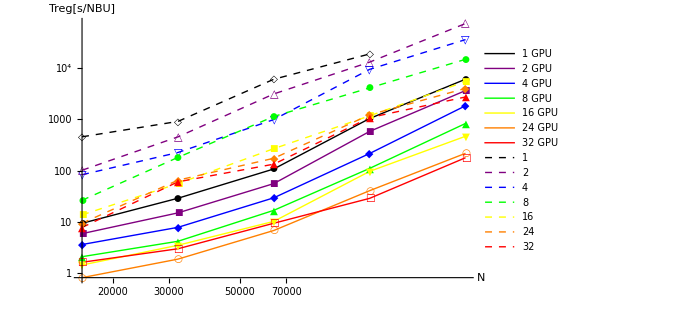
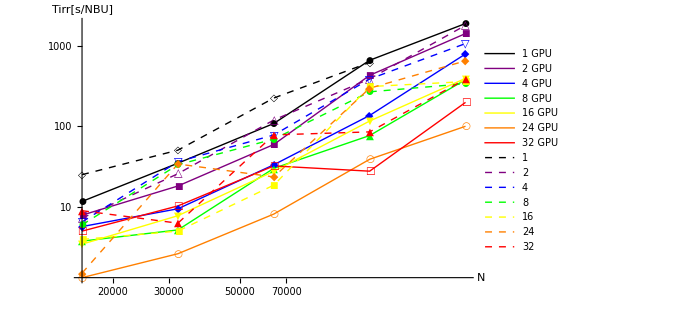
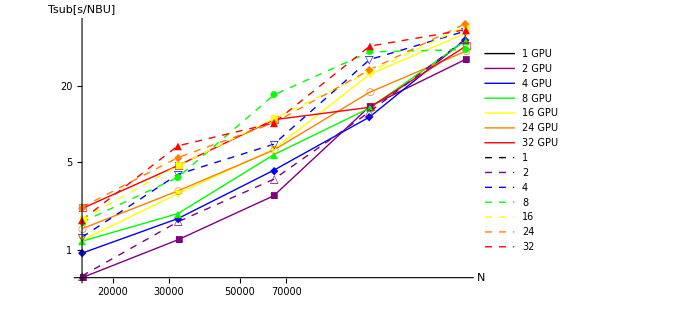

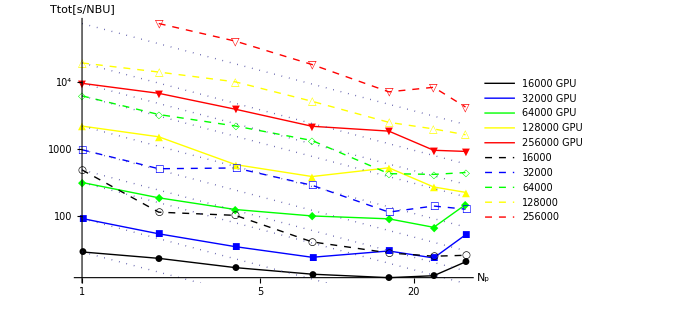
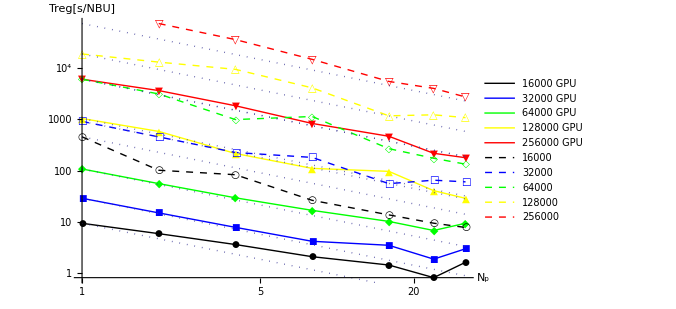
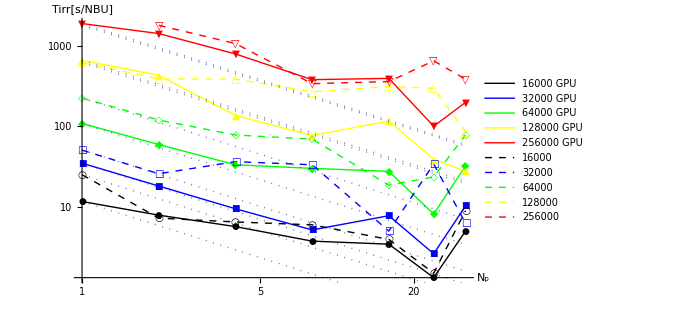
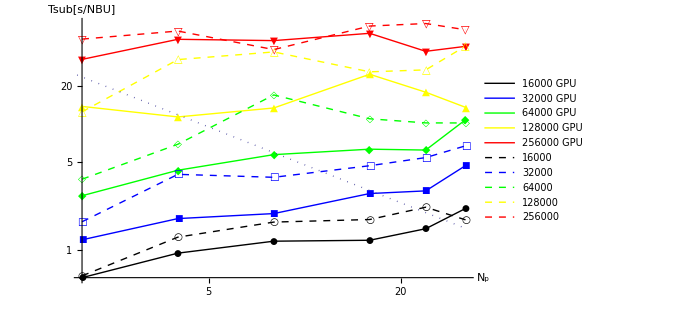

```mathematica
nsl={1,2,4,8,16,24,32};
plist1[d_]:=Table[Select[d,#[[1]]==i&][[All,2;;3]],{i,nsl}];
p1style=Flatten[Transpose@Table[{i,{i,Dashed}},{i,{Black,Purple,Blue,Green,Yellow,Orange,Red}}],1];
exp1=Table[ListLogLogPlot[plist1[dd[[j]]]~Join~plist1[ddc[[j]]],PlotLegends->LineLegend[p1style,Flatten[{#"GPU",#}&@(ToString/@nsl)]],PlotStyle->p1style,PlotMarkers->Automatic,PlotRange->All,ImageSize->500,Joined->True,AxesLabel->{"N",dlabel[[j]]~~"[s/NBU]"}],{j,4}]
ns2={16000,32000,64000,128000,256000};
plist2[d_]:=Table[Select[d,#[[2]]==i&][[All,{1,3}]],{i,ns2}]
eplinear[d_]:=Table[Select[d,#[[2]]==i&][[1,3]]/x,{i,{16000,32000,64000,128000,256000}}]
p2style=Flatten[Transpose@Table[{i,{i,Dashed}},{i,{Black,Blue,Green,Yellow,Red}}],1];
exp2=Table[ListLogLogPlot[plist2[dd[[j]]]~Join~plist2[ddc[[j]]],PlotLegends->LineLegend[p2style,Flatten[{#"GPU",#}&@(ToString/@ns2)]],PlotMarkers->Automatic,PlotStyle->p2style,PlotRange->All,Epilog->First@LogLogPlot[eplinear[dd[[j]]]~Join~eplinear[ddc[[j]]],{x,1,32},PlotStyle->Dotted],ImageSize->500,Joined->True,AxesLabel->{"N_p",dlabel[[j]]~~"[s/NBU]"}],{j,4}]
```

```mathematica
columnlist={4,5,6,8,9,11,12,13,14,15};
exp3=Column[{"From inside to outside: N = 16k, 32k, 64k, 128k, 256k",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[data,#[[1]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,{2,4,8,16,24,32}}]},Center]
exp4=Column[{"From inside to outside: N_proc = 2, 4, 8, 16, 24, 32",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[data,#[[2]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,{16000,32000,64000,128000,256000}}]},Center]
exp5=Column[{"From inside to outside No GPU: N = 16k, 32k, 64k, 128k, 256k",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[datac,#[[1]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,{2,4,8,16,24,32}}]},Center]
exp6=Column[{"From inside to outside No GPU: N_proc = 2, 4, 8, 16, 24, 32",
Table[Column[{"N_proc="~~ToString[i],
PieChart[Select[datac,#[[2]]==i&][[All,columnlist]],ChartLegends->label[[columnlist]]]},Center],{i,{16000,32000,64000,128000,256000}}]},Center]
```

From inside to outside: N = 16k, 32k, 64k, 128k, 256k
{N_proc=2
-Graphics-,N_proc=4
-Graphics-,N_proc=8
-Graphics-,N_proc=16
-Graphics-,N_proc=24
-Graphics-,N_proc=32
-Graphics-}

From inside to outside: N_proc = 2, 4, 8, 16, 24, 32
{N_proc=16000
-Graphics-,N_proc=32000
-Graphics-,N_proc=64000
-Graphics-,N_proc=128000
-Graphics-,N_proc=256000
-Graphics-}

From inside to outside No GPU: N = 16k, 32k, 64k, 128k, 256k
{N_proc=2
-Graphics-,N_proc=4
-Graphics-,N_proc=8
-Graphics-,N_proc=16
-Graphics-,N_proc=24
-Graphics-,N_proc=32
-Graphics-}

From inside to outside No GPU: N_proc = 2, 4, 8, 16, 24, 32
{N_proc=16000
-Graphics-,N_proc=32000
-Graphics-,N_proc=64000
-Graphics-,N_proc=128000
-Graphics-,N_proc=256000
-Graphics-}

```mathematica
Export["/Users/wanglong/data/Nb6Test/t_n.eps",exp1]
Export["/Users/wanglong/data/Nb6Test/t_np.eps",exp2]
Export["/Users/wanglong/data/Nb6Test/f_n.eps",exp3]
Export["/Users/wanglong/data/Nb6Test/f_np.eps",exp4]
Export["/Users/wanglong/data/Nb6Test/f_n_ngpu.eps",exp5]
Export["/Users/wanglong/data/Nb6Test/f_np_ngpu.eps",exp6]
```

/Users/wanglong/data/Nb6Test/t_n.eps

/Users/wanglong/data/Nb6Test/t_np.eps

/Users/wanglong/data/Nb6Test/f_n.eps

/Users/wanglong/data/Nb6Test/f_np.eps

/Users/wanglong/data/Nb6Test/f_n_ngpu.eps

/Users/wanglong/data/Nb6Test/f_np_ngpu.eps

```mathematica
ExpandFileName["/Users/wanglong/data/Nb6Test/f_np.eps"]
```

/Users/wanglong/data/Nb6Test/f_np.eps

```mathematica
datat=Table[Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/time."~~ToString[i],"Table"],#[[1;;2]]=={j,128000}&][[1]],{i,0,10}],{j,{1,2,4,8,16,24,32}}];
```

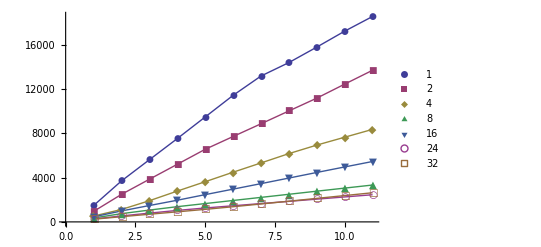

```mathematica
ListPlot[datat[[All,All,3]],Joined->True,PlotMarkers->Automatic,PlotLegends->{1,2,4,8,16,24,32}]
```

```mathematica
datalist=Import["/Users/wanglong/Dropbox/Datas/Nb6Test/temp.lst","Table"][[1;;-2]];
data1l1=Select[datalist,#[[5]]==0&];
```

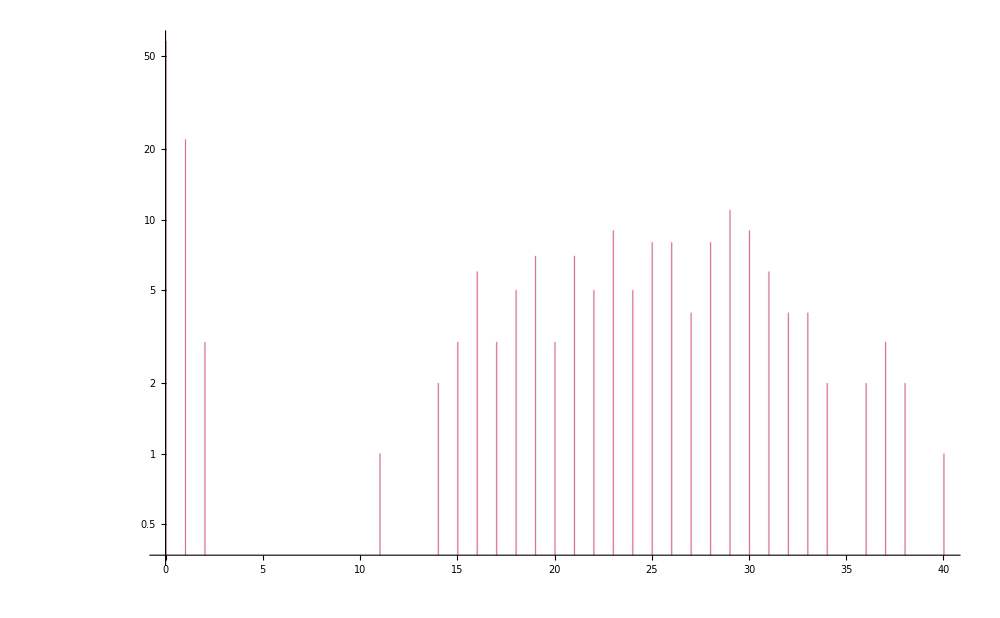

```mathematica
Histogram[Select[datalist[[All,8]],#<100&],1024,"LogCount",ImageSize->1000,ChartStyle->Red]
```

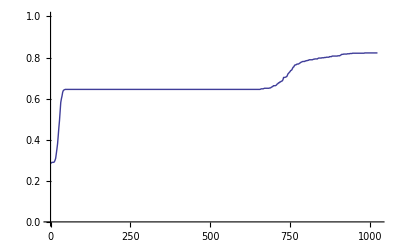

```mathematica
ListPlot[Table[{2*i,Length[Select[datalist,#[[8]]<2*i&]]/Length[datalist]//N},{i,512}],Joined->True,PlotRange->{0,1}]
```

```mathematica
ddd=Import[]
```